# Cuaderno de Prácticas

## Análisis y métodos numéricos

## Grado en Ingeniería Informática

## CURSO 2024/25

## Datos personales

Nombre y apellidos : Francisco Javier Martín - Lunas Escobar
DNI : 26268082
Grupo de teoría : 2
Grupo de prácticas :

## Tema 1. Números reales

### Problemas de ecuaciones con valor absoluto

## 1.- Resolver ||x-1|-1|=1 Enero 18

### Problemas de inecuaciones con valor absoluto

## 1.- Resolver ||x-1|-1|<1 Octubre 2021

Solución:
Si el valor absoluto de una expresión vale menos de un número positivo a, entonces la expresión está entre -a y a. Sabiendo esto obtenemos:
	 ||x-1|-1|<1 ⟹ -1<|x-1|-1<1 ⟹(sumando 1 en cada término) ⟹ 0<|x-1|< 2 
Es decir, deben cumplirse las dos condiciones:
	0<|x-1|
	|x-1|< 2 
La primera desigualdad significa que x es distinto de 1, x ≠1,  y la segunda que  -2<x-1<2 .

En resumen,  x ≠1  y -1< x <3.

Por tanto, las soluciones son los números de los intervalos (-1,1) y (1,3).

Con el Mathematica

```mathematica
Reduce[Abs[Abs[x-1]-1]<1,x,Reals]
```

-1<x<1||1<x<3

### Problemas de inducción

## 1.- Demostrar, usando inducción, que 1*2 + 2*3 + 3*4 + ...+ n(n+1) = (n(n+1)(n+2))/3 para n = 1, 2, 3, 4, ... Julio-Octubre 18

Solución:
Para realizar la demostración por inducción, comenzamos estudiando el primer caso, n=1. 
El primer término, que empieza con 1*2, debe terminar cuando n=1 con 1*(1+1), por tanto se reduce a un sumando. La igualdad que habría que comprobar es:
1*2  = (1(1+1)(1+2))/3. Es inmediato comprobar que ambas expresiones valen 2.
En la segunda parte del método de inducción, se supone que la propiedad es cierta para un valor n y se trata de comprobar que también lo es para (n+1).

Es decir, si la igualdad es cierta para n, 1*2 + 2*3 + 3*4 + ...+ n(n+1) = (n(n+1)(n+2))/3, se trataría de demostrar que también lo será para (n+1).

El primer termino de la expresión para (n+1) es:
1*2 + 2*3 + 3*4 + ...+ n(n+1)+ (n+1)(n+1+1) =1*2 + 2*3 + 3*4 + ...+ n(n+1)+ (n+1)(n+2) 

El segundo término de la expresión para n+1 es
 ((n+1)((n+1)+1)((n+1)+2))/3 = ((n+1)(n+2)(n+3))/3
Tenemos que demostrar que si es cierto para n, también lo es para n+1, es decir que si  1*2 + 2*3 + 3*4 + ...+ n(n+1) = (n(n+1)(n+2))/3 también será cierto que
	1*2 + 2*3 + 3*4 + ...+ n(n+1)+ (n+1)(n+2) =((n+1)(n+2)(n+3))/3
Observamos que los primeros sumandos de la primera expresión son los de la expresión para n, por tanto,
 1*2 + 2*3 + 3*4 + ...+ n(n+1)+ (n+1)(n+2) =(n(n+1)(n+2))/3 + (n+1)(n+2) = (n+1)(n+2)(n/3+1) =(n+1)(n+2)((n+3)/3) = ((n+1)(n+2)(n+3))/3
 y concluimos que de ser cierta la igualdad para n, también lo es para (n+1).

### Otros problemas

## 1.- Razonar cuál de los siguientes números es racional y expresarlo como cociente de dos números enteros: 0,010101010101... = ∑_(n=1)^∞ 1/10^(2n) , 0,1001000010000001.... = ∑_(n=1)^∞ 1/(10^(n^2)) . Julio 2023

Comentarios:
Los números racionales son los cocientes de números enteros, a/b, con b>0. Al realizar la división de a entre b, puede obtenerse un número entero, en otro caso, para obtener una forma numérica decimal, “sacamos decimales” y tiene que llegar un momento en que los restos posibles (que serán números entre 0 y b-1) se tienen que repetir de forma indefinida y se origina un periodo. De igual forma, si un número tiene un desarrollo decimal, donde a partir de un momento, una sucesión de cifras se repite sucesivamente y de forma indefinida, podemos expresar el número como cociente de dos enteros. 
Además de los racionales, hay más números, algunos utilizados con mucha frecuencia como la raíz de dos, el número π, el logaritmo de 2, etc. Estos números forman parte de los irracionales, números reales que no son racionales. Estos números no tienen un desarrollo decimal periódico.

Solución:
Observamos que el primer número es periódico. El par de cifras 01 se repite continuamente. Se trata de un número racional. Para ponerlo como fracción escribimos
				x = 0,01010101...   
			100 x = 1,01010101...
Restando de la segunda expresión la primera:  99 x = 1. Por tanto, x=1/99.

El segundo número tiene un desarrollo decimal que no es periódico. Hay dos ceros entre los primeros dos unos, luego hay cuatro ceros, después seis ceros, etc. No es un número racional.
 
Con el Mathematica sería:

```mathematica
Sum[1/10^(2n),{n,1,Infinity}]
```

1/99

```mathematica
Sum[1/10^(n^2),{n,1,Infinity}]
```

1/2 (-1+EllipticTheta[3,0,1/10])

## 5.- Expresar el número 12’345454545... como cociente de dos números enteros. Julio 22

Llamando               x=12’345454545... 
Tenemos que 10 x = 123’45454545... 
También       1000x = 12345’454545...
Restando, 1000x - 10x = 12345-123. Por tanto, 990 x = 12222, x=12222/990.  Si queremos simplificar, que no es necesario, dividimos numerador y denominador por 2 y por 9. 12222/990 = 1358/110 = 679/55.

Otra forma sería escribir el número como una suma con una serie geométrica (y aplicar la fórmula para la suma en este caso).

12’3454545... = 12 +  3/10+ ∑_(n=1)^∞ 45/(10*100^n) = 120/10 +  3/10+45/10 ∑_(n=1)^∞ 1/100^n = 123/10 +45/10 (1/100)/(1-1/100) = 123/10 +45/10 1/(100-1) = 123/10 +45/10 1/99 = 123/10 +45/990 = 123/10 +5/110 = 123/10 +1/22 = (123*22+10)/220 =  2716/220= 2716/220 = 679/55

## 1.- Obtener los valores de x para los que x^2 < |x|. Expresar el conjunto por medio de intervalos, decir si es abierto o cerrado, si está acotado superior o inferiormente, si tiene máximo o mínimo, supremo o ínfimo. Enero 2019

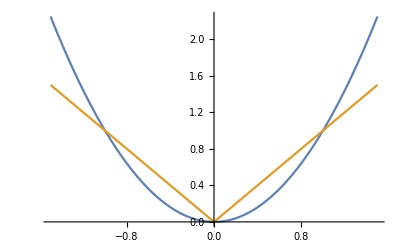
Solución: 	
El valor absoluto de x puede ser x ó -x, según sea x mayor o menor que cero. Distinguimos los dos casos:
	Cuando x es mayor que cero, la desigualdad queda como:  x^2 < |x|=x . Estudiaremos la desigualdad:   x^2 < x . Restando x,   x^2-x<0 ⟹ x(x-1)<0. Como x>0 ⟹ x-1 debe ser menor que 0 ⟹ x<1
	
	Cuando x es menor que cero,  la desigualdad queda como:  x^2 < |x|=-x . Estudiaremos la desigualdad:   x^2 < -x . Sumando x,   x^2+x<0 ⟹ x(x+1)<0. Como x<0 ⟹ x+1 debe ser mayor que 0 ⟹ x>-1
	
En el caso x=0, no se cumple la desigualdad.

Por tanto, cuando x es mayor que cero, debe ser menor que 1 y cuando x es menor que cero, debe ser mayor que -1. Luego el conjunto es (-1,0) ∪ (0,1). 
Se trata de un conjunto abierto, acotado superior e inferiormente, el supremo es 1, el ínfimo es -1, no tiene máximo, ni mínimo.

Si dibujamos las gráficas de las dos funciones:
			-Graphics-
Vemos que el valor absoluto está por encima de la gráfica de x^2 cuando x está en (-1,0) y en (0,1).
 
Con el Mathematica,

```mathematica
Reduce[x^2<Abs[x],x,Reals]
```

-1<x<0||0<x<1

## Tema 2. Números complejos